# Measuring Ω_M in a Λ-M Universe

## Calculations for problem 8

### Downloading Supernovae Redshifts, Magnitudes, and Errors

```mathematica
Needs["ErrorBarPlots`"];
Temp=Transpose[Import["http://supernova.lbl.gov/Union/figures/SCPUnion2.1_mu_vs_z.txt","Data"][[6;;585]]][[{2,3,4}]];

RedS=Temp[[1]];
Mags=Temp[[2]];
MagE=Temp[[3]];

PlotData=Thread[{Thread[{RedS,Mags}],Thread[ErrorBar[MagE]]}];
```

### Plotting the Magnitudes of Supernovae as a function of redshift with Errors

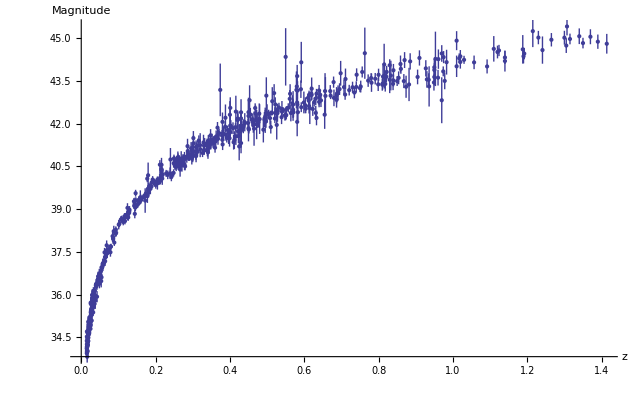

```mathematica
ErrorListPlot[PlotData,AxesLabel->{"z","Magnitude"}]
```

### Goodness of Fit Test on the Data

```mathematica
Num = 1000;

MDens = {};
χ2={};

For[i=0,i≤Num,i++,
Ωm=N[i/Num];
MDens=Append[MDens,Ωm];
Residuals={};
For[j=1,j≤Length[Mags],j++,
Residuals=Append[Residuals,Log[10,((1+RedS[[j]])*NIntegrate[Sqrt[1+Ωm*x*(3+3x+x^2)]^-1,{x,0,RedS[[j]]}])^5*10^-Mags[[j]]]]
];
χ2=Append[χ2,Total[Residuals^2/MagE^2]-Total[Residuals/MagE^2]^2/Total[MagE^-2]];
]
```

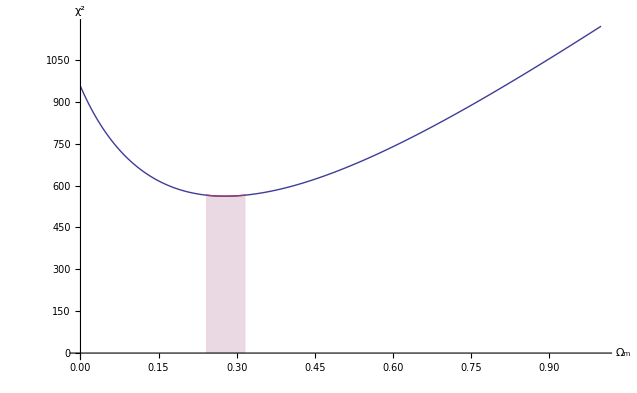

{0.278,562.227}

{0.241,0.317}

```mathematica
GoodPos =Flatten[Position[χ2,x_/;x<=Min[χ2]+3.84]];
GoodΩ=Thread[MDens[[GoodPos]]];
Goodχ = Thread[χ2[[GoodPos]]];

ListPlot[{Thread[{MDens,χ2}],Thread[{GoodΩ,Goodχ}]},AxesLabel->{"Ω_m","χ^2"},PlotRange->Full,Joined->{True,True},Filling->{2->Axis}]
{MDens[[Flatten[Position[χ2,Min[χ2]]][[1]]]],Min[χ2]}
{Min[GoodΩ],Max[GoodΩ]}
```

The data has a minimum χ^2value of 562.227 at Ω_m=.278. The 95% confidence interval is [.241,.317].